```mathematica
<<PlotLegends`
cana120150817=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\cana\\1_20150817.xlsx"];
cana120151019=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\cana\\1_20151019.xlsx"];
cana220150817=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\cana\\2_20150817.xlsx"];
cana220151019=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\cana\\2_20151019.xlsx"];
cana320150817=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\cana\\3_20150817.xlsx"];
cana320151019=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\cana\\3_20151019.xlsx"];
tempo=Table[cana120150817[[1,i,1]],{i,1,Length[cana120150817[[1]]]}];
transp120150817=Table[cana120150817[[1,i,2]],{i,1,Length[cana120150817[[1]]]}];
transp120151019=Table[cana120151019[[1,i,2]],{i,1,Length[cana120151019[[1]]]}];
transp220150817=Table[cana220150817[[1,i,2]],{i,1,Length[cana220150817[[1]]]}];
transp220151019=Table[cana220151019[[1,i,2]],{i,1,Length[cana220151019[[1]]]}];
transp320150817=Table[cana320150817[[1,i,2]],{i,1,Length[cana320150817[[1]]]}];
transp320151019=Table[cana320151019[[1,i,2]],{i,1,Length[cana320151019[[1]]]}];
par120150817=Table[cana120150817[[1,i,3]],{i,1,Length[cana120150817[[1]]]}];
par120151019=Table[cana120151019[[1,i,3]],{i,1,Length[cana120151019[[1]]]}];
par220150817=Table[cana220150817[[1,i,3]],{i,1,Length[cana220150817[[1]]]}];
par220151019=Table[cana220151019[[1,i,3]],{i,1,Length[cana220151019[[1]]]}];
par320150817=Table[cana320150817[[1,i,3]],{i,1,Length[cana320150817[[1]]]}];
par320151019=Table[cana320151019[[1,i,3]],{i,1,Length[cana320151019[[1]]]}];
dpv120150817=Table[cana120150817[[1,i,4]],{i,1,Length[cana120150817[[1]]]}];
dpv120151019=Table[cana120151019[[1,i,4]],{i,1,Length[cana120151019[[1]]]}];
dpv220150817=Table[cana220150817[[1,i,4]],{i,1,Length[cana220150817[[1]]]}];
dpv220151019=Table[cana220151019[[1,i,4]],{i,1,Length[cana220151019[[1]]]}];
dpv320150817=Table[cana320150817[[1,i,4]],{i,1,Length[cana320150817[[1]]]}];
dpv320151019=Table[cana320151019[[1,i,4]],{i,1,Length[cana320151019[[1]]]}];
transpVsTempo120150817=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],transp120150817[[i]]},{i,1,Length[tempo]}]]]];
transpVsTempo120151019=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],transp120151019[[i]]},{i,1,Length[tempo]}]]]];
transpVsTempo220150817=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],transp220150817[[i]]},{i,1,Length[tempo]}]]]];
transpVsTempo220151019=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],transp220151019[[i]]},{i,1,Length[tempo]}]]]];
transpVsTempo320150817=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],transp320150817[[i]]},{i,1,Length[tempo]}]]]];
transpVsTempo320151019=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],transp320151019[[i]]},{i,1,Length[tempo]}]]]];
parVsTempo120150817=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],par120150817[[i]]},{i,1,Length[tempo]}]]]];
parVsTempo120151019=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],par120151019[[i]]},{i,1,Length[tempo]}]]]];
parVsTempo220150817=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],par220150817[[i]]},{i,1,Length[tempo]}]]]];
parVsTempo220151019=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],par220151019[[i]]},{i,1,Length[tempo]}]]]];
parVsTempo320150817=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],par320150817[[i]]},{i,1,Length[tempo]}]]]];
parVsTempo320151019=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],par320151019[[i]]},{i,1,Length[tempo]}]]]];
dpvVsTempo120150817=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],dpv120150817[[i]]},{i,1,Length[tempo]}]]]];
dpvVsTempo120151019=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],dpv120151019[[i]]},{i,1,Length[tempo]}]]]];
dpvVsTempo220150817=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],dpv220150817[[i]]},{i,1,Length[tempo]}]]]];
dpvVsTempo220151019=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],dpv220151019[[i]]},{i,1,Length[tempo]}]]]];
dpvVsTempo320150817=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],dpv320150817[[i]]},{i,1,Length[tempo]}]]]];
dpvVsTempo320151019=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],dpv320151019[[i]]},{i,1,Length[tempo]}]]]];
```

## Cana - 17/08/2015 - Transpiração

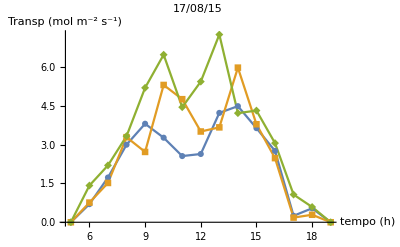

```mathematica
g1=ListLinePlot[{transpVsTempo120150817,transpVsTempo220150817,transpVsTempo320150817},PlotLegend->{"-0.18MPa","-0.17MPa","-0.16MPa"},LegendPosition->{.7,-0.4},PlotLabel->"17/08/15",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","Transp (mol m^-2 s^-1)"}]
```

## Cana - 19/10/2015 - Transpiração

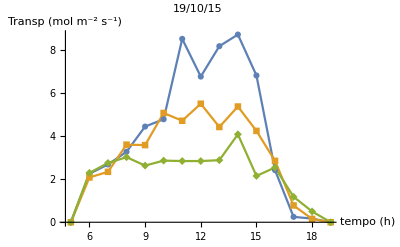

```mathematica
g2=ListLinePlot[{transpVsTempo120151019,transpVsTempo220151019,transpVsTempo320151019},PlotLegend->{"-0.14MPa","-0.15MPa","-0.16MPa"},LegendPosition->{.7,-0.4},PlotLabel->"19/10/15",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","Transp (mol m^-2 s^-1)"}]
```

## Cana - 17/08/2015 - PAR ( radiação fotossinteticamente ativa)

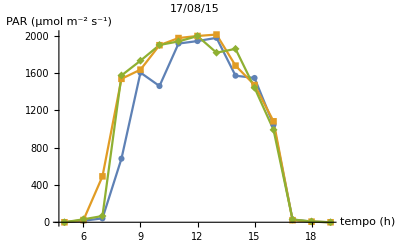

```mathematica
g3=ListLinePlot[{parVsTempo120150817,parVsTempo220150817,parVsTempo320150817},PlotLegend->{"-0.18MPa","-0.17MPa","-0.16MPa"},LegendPosition->{.7,-0.4},PlotLabel->"17/08/15",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","PAR (μmol m^-2 s^-1)"}]
```

## Cana - 19/10/2015 - PAR ( radiação fotossinteticamente ativa)

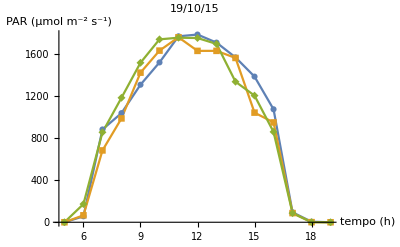

```mathematica
g4=ListLinePlot[{parVsTempo120151019,parVsTempo220151019,parVsTempo320151019},PlotLegend->{"-0.14MPa","-0.15MPa","-0.16MPa"},LegendPosition->{.7,-0.4},PlotLabel->"19/10/15",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","PAR (μmol m^-2 s^-1)"}]
```

## Cana - 17/08/2015 - DPV (déficit de pressão de vapor)

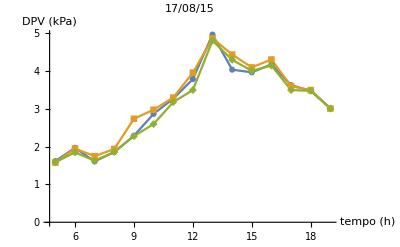

```mathematica
g5=ListLinePlot[{dpvVsTempo120150817,dpvVsTempo220150817,dpvVsTempo320150817},PlotLegend->{"-0.18MPa","-0.17MPa","-0.16MPa"},LegendPosition->{.7,-0.4},PlotLabel->"17/08/15",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","DPV (kPa)"}]
```

## Cana - 19/10/2015 - DPV (déficit de pressão de vapor)

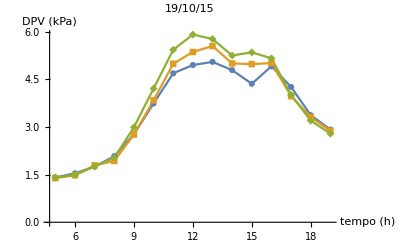

```mathematica
g6=ListLinePlot[{dpvVsTempo120151019,dpvVsTempo220151019,dpvVsTempo320151019},PlotLegend->{"-0.14MPa","-0.15MPa","-0.16MPa"},LegendPosition->{.7,-0.4},PlotLabel->"19/10/15",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","DPV (kPa)"}]
```